```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model -> "./modelFiles/SMS-stop_FA/SMS-stop_FA"];
```

```mathematica
processHGG = { V[4],V[4]} -> {S[1]};
tops = CreateTopologies[1, 2->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

```mathematica
allDiags = InsertFields[tops, processHGG,InsertionLevel-> {Particles},ExcludeParticles->{F[12],V[1],V[2],V[3]}];
FR$ClassesTranslation
```

generic model {Lorentz} initialized

classes model {./modelFiles/SMS-stop_FA/SMS-stop_FA} initialized

in total: 2 Particles insertions

{A→V(1),Z→V(2),W→V(3),G→V(4),ghA→U(1),ghZ→U(2),ghWp→U(3),ghWm→U(4),ghG→U(5),ve→F(1),vm→F(2),vt→F(3),e→F(4),mu→F(5),ta→F(6),u→F(7),c→F(8),t→F(9),d→F(10),s→F(11),b→F(12),H→S(1),G0→S(2),GluonPropagator→S(3),chi→F(13),ST→S(4)}

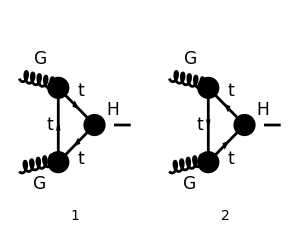

```mathematica
Paint[allDiags,ColumnsXRows->{2,1},PaintLevel->{Particles},ImageSize->{300,250},Numbering->Simple];
```

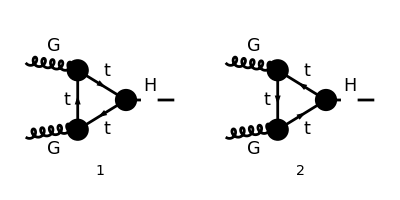

```mathematica
diags=DiagramExtract[allDiags,{1,2}];
Paint[diags,ColumnsXRows->{2,1},ImageSize->{400,200},Numbering->Simple];
```

```mathematica
(* Set Truncated->True to remove external fields  *)
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1,Truncated->True],IncomingMomenta->{p1,p2},OutgoingMomenta->{k},LoopMomenta->{q},List->False,TransversePolarizationVectors->{p1,p2},DropSumOver->True,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 2 Particles amplitudes

(ⅈ tr((γ·(-k+p2+q)+MT).(-(ⅈ yt)/(√2)).(MT+γ·(p2+q)).(-2 ⅈ √π √aS γ^ν T_Col4Col5^Glu2).(MT+γ·q).(-2 ⅈ √π √aS γ^μ T_Col5Col4^Glu1)))/((q^2-MT^2).((p2+q)^2-MT^2).((-k+p2+q)^2-MT^2))+(ⅈ tr((γ·(-k+p2+q)+MT).(-(ⅈ yt)/(√2)).(MT+γ·(p2+q)).(2 ⅈ √π √aS γ^ν T_Col5Col4^Glu2).(MT+γ·q).(2 ⅈ √π √aS γ^μ T_Col4Col5^Glu1)))/((q^2-MT^2).((p2+q)^2-MT^2).((-k+p2+q)^2-MT^2))

```mathematica
PT =1/2( MTD[μ,ν]-FVD[p1,ν]FVD[p2,μ]/ScalarProduct[p1,p2]);
```

```mathematica
FCClearScalarProducts[];
ScalarProduct[k,k]=s;
ScalarProduct[p1,p1]=0;
ScalarProduct[p2,p2]=0;
ScalarProduct[p1,p2]=s/2;
ScalarProduct[k,p2]=s/2;
ScalarProduct[k,p1]=s/2;
```

```mathematica
amp[1]=Contract[PT SUNSimplify[FCTraceFactor[ amp[0]]]]//Simplify
```

(√2 π aS yt δ^Glu1Glu2 (2 tr((MT-γ·(k-p2-q)).(MT+γ·(p2+q)).(γ·p1).(MT+γ·q).(γ·p2))-s tr((MT-γ·(k-p2-q)).(MT+γ·(p2+q)).γ^ν.(MT+γ·q).γ^ν)))/(s (q^2-MT^2).((p2+q)^2-MT^2).((k-p2-q)^2-MT^2))

```mathematica
amp[2]=FullSimplify[DiracSimplify[amp[1]]]
```

(2 √2 π aS MT yt δ^Glu1Glu2 (s (-2 (D-1) MT^2+2 (D-5) q^2+(D-2) s-4 (p2·q))+4 s (k·q)-4 (p1·q) (s-4 (p2·q))))/(s (q^2-MT^2).((p2+q)^2-MT^2).((k-p2-q)^2-MT^2))

```mathematica
amp[3]=TID[amp[2],q,ToPaVe->True]//Simplify
```

-2 ⅈ √2 π^3 aS MT yt δ^Glu1Glu2 ((8 MT^2-(D-2) s) C_0(0,0,s,MT^2,MT^2,MT^2)-2 (D-4) B_0(s,MT^2,MT^2))

```mathematica
(* Make sure there are no divergences *)
UVpart = PaXEvaluateUV[amp[3]]
```

0

```mathematica
amp[4]=ChangeDimension[amp[3],4]/.{D->4}//Simplify
```

-4 ⅈ √2 π^3 aS MT yt (4 MT^2-s) δ^Glu1Glu2 C_0(0,0,s,MT^2,MT^2,MT^2)

```mathematica
amp[5]=Simplify[PaXEvaluate[amp[3],PaXC0Expand->True,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)],Assumptions-> {s>0,MT>0}]
```

-(ⅈ aS MT yt δ^Glu1Glu2 ((4 MT^2-s) log^2((√(s (s-4 MT^2))+2 MT^2-s)/(2 MT^2))+4 s))/(4 √2 π s)

#### Check Final Result:

```mathematica
resCheck=Simplify[amp[5]//.{s-> 4 MT^2/ρ,yt-> MT/Subscript[v, H],Subscript[v, H]-> 1/(√(√2 Subscript[G, F]))},Assumptions->{ρ>0,MT>0}]
```

-(ⅈ aS MT^2 √G_F ((ρ-1) log^2((ρ+2 √(1-ρ)-2)/ρ)+4) δ^Glu1Glu2)/(4 2^(1/4) π)

Correct answer (check Eq. 2.5 and 2.6  from S. Bock thesis) for ρ > 1:

```mathematica
answer1=(-I(SUNTrace[SUNT[Glu1,Glu2]]))/(4 Pi)√(√2 Subscript[G, F])aS MT (2 MT +MT (4 MT^2 - MH^2)(1/(2 MH^2))(Log[(1+√(1-ρ))/(1-√(1-ρ))]-I Pi)^2)/.{MH-> √(4 MT^2/ρ)}//
Simplify
```

-(ⅈ aS MT^2 √G_F (4+(ρ-1) (log((√(1-ρ)+1)/(1-√(1-ρ)))-ⅈ π)^2) δ^Glu1Glu2)/(8 2^(3/4) π)

```mathematica
(* Not sure where the 2 √2 factor comes from *)
FullSimplify[resCheck-2 √2 answer1,Assumptions->{ρ<1,ρ>0}]
```

0

#### EFT Limit (MT → ∞)

```mathematica
Series[resCheck/.ρ-> 4 MT^2/MH^2,{MT, Infinity,1}]
```

-(ⅈ aS MH^2 √G_F δ^Glu1Glu2)/(6 2^(1/4) π)+O((1/MT)^2)

#### Expansion using Package - X

```mathematica
Collect[Expand[PaXEvaluate[amp[3],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries-> {{s,0,2}}]],s,Simplify]
```

-(7 ⅈ aS s^2 yt δ^Glu1Glu2)/(720 √2 π MT^3)-(ⅈ aS s yt δ^Glu1Glu2)/(6 √2 π MT)